# Temas de física 4: PC1

```mathematica
ClearAll["Global`*"]
```

## Definiendo funciones para graficar las singularidades, los retratos de fase y otras cosas para el análisis cualitativo

```mathematica
LinCam[f_,g_,n_:3]:=StreamDensityPlot[{f[x,y],g[x,y]},{x,-1*n,n},{y,-1*n,n},ColorFunction->"Pastel",VectorColorFunction->Black];(*Esta función grafica los stramlines*)
```

```mathematica
initialp[f_,g_]:=ArrayReshape[Table[NDSolve[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==i,y[0]==j},{x[t],y[t]},{t,-20,20},MaxSteps->Infinity],{i,-8,8,4},{j,-8,8,4}],{24,2}] (*Esta función produce un array de las soluciones de los sistemas de ecuaciones para 24 valores iniciales*)
```

```mathematica
RetFas[f_,g_]:=ParametricPlot[Evaluate[Table[{x[t],y[t]}/.initialp[f,g][[i]],{i,24}]],{t,-20,20},PlotStyle->Directive[AbsoluteThickness[1.5],RGBColor[1,0.5,0.6]], PlotRange->{{-3,3},{-3,3}},PlotPoints->1000,AxesLabel->{"x","y"}]; (*Esta función grafica trayectorias utilizando el array producido por la función anterior*)
```

```mathematica
EigenVec[E_]:=Plot[{ (E[[1]][[2]])/(E[[1]][[1]])*x,(E[[2]][[2]])/(E[[2]][[1]])*x},{x,-15,15},PlotStyle->Directive[AbsoluteThickness[2.0],White]]; (*Esta función grafica las rectas que tienen la dirección de los autovectores*)
```

```mathematica
Showing[g1_,g2_,g3___]:=Show[{g1,g2,g3},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema autónomo"],Axes->True,Frame->True,Epilog->{PointSize[0.02],{RGBColor[0.5,0.5,0.6],Point[{0,0}]}},ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

## Pregunta 2 : Analiza en forma cualitativa y establecer el retrato de fase para los sistemas

a)Piecewise[{{ẋ, =3x+4y}, {ẏ, =4x-3y}}]

Definiendo las funciones componentes del campo vectorial asociado al sistema:

```mathematica
f1[x_,y_]:=3x+4y;
```

```mathematica
g1[x_,y_]:=4x-3y;
```

Ubicando las singularidades:

```mathematica
Solve[{f1[x,y]==0,g1[x,y]==0}]
```

{{x→0,y→0}}

En este caso solo hay una singularidad y esta en el origen.
		Analizando la estabilidad del origen, de acuerdo a la naturaleza de los vectores propios de la matriz A del sistema autónomo:

```mathematica
A1=({{3, 4}, {4, -3}});
```

```mathematica
Eigenvalues[A1]
```

{-5,5}

Observamos que los autovalores son de signos opuestos, por lo cual deducimos que la singularidad del origen es de tipo silla.

```mathematica
Eigenvectors[A1]
```

{{-1,2},{2,1}}

```mathematica
G1=LinCam[f1,g1,10]; (*Graficando lineas de corriente Streamlines*)
```

```mathematica
G2=RetFas[f1,g1]; (*Graficando el ciertas soluciones - Retrato de fase*)
```

```mathematica
G3=EigenVec[Eigenvectors[A1]]; (*Graficando los autovectores*)
```

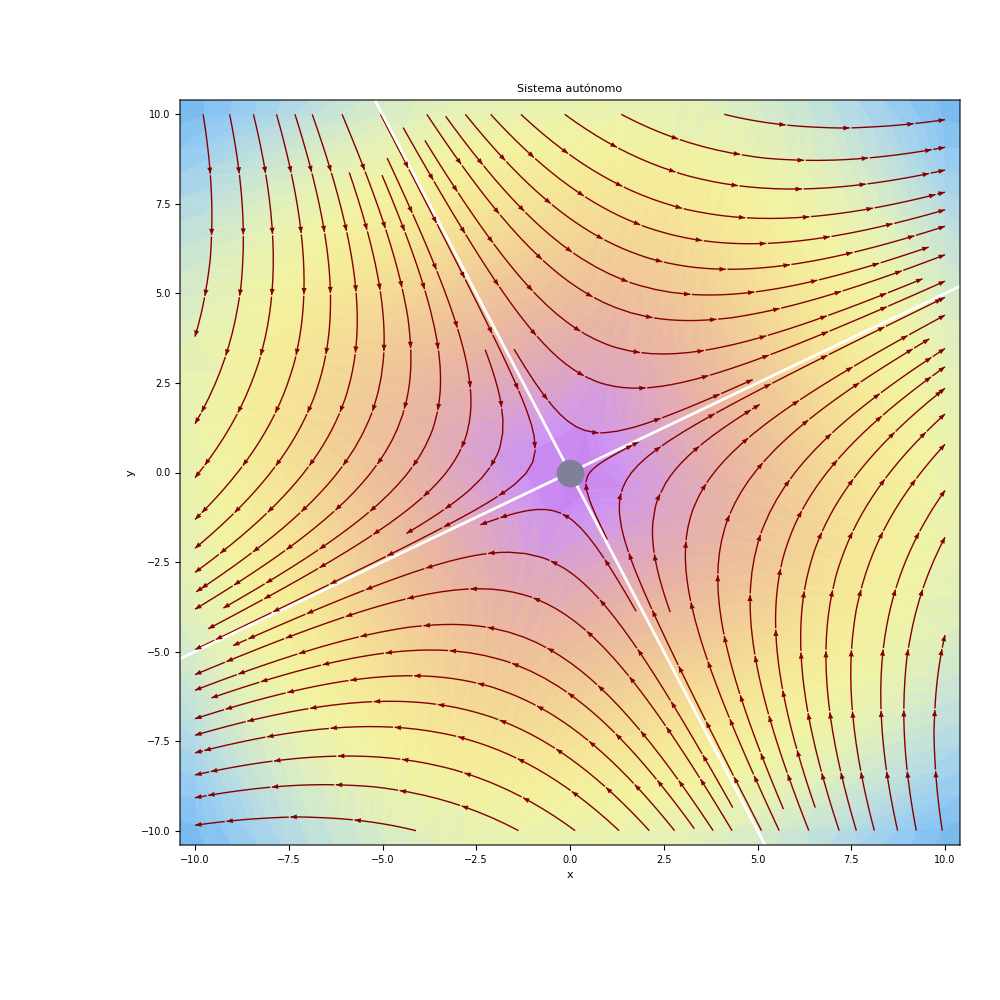

```mathematica
Showing[G1,G2,G3](*Graficando el Retrato de fase, las rectas de los autovectores y la singularidad*)
```

b)Piecewise[{{ẋ, =-0.5x+y}, {ẏ, =-x+y}}]

Definiendo las funciones componentes del campo vectorial asociado al sistema:

```mathematica
f2[x_,y_]:=-0.5x+y;
```

```mathematica
g2[x_,y_]:=-x+y;
```

Ubicando las singularidades:

```mathematica
Solve[{f2[x,y]==0,g2[x,y]==0}]
```

{{x→0.,y→0.}}

En este caso solo hay una singularidad y esta en el origen.
		Analizando la estabilidad del origen, de acuerdo a la naturaleza de los vectores propios de la matriz A del sistema autónomo:

```mathematica
A2=({{-0.5, 1}, {-1, 1}});
```

```mathematica
Eigenvalues[A2]
```

{0.25+0.661438 ⅈ,0.25-0.661438 ⅈ}

Observamos que los autovalores son complejos de valores conjugados y la parte real es positiva, por lo cual deducimos que la singularidad del 
		origen es de tipo foco espiral inestable.

```mathematica
Eigenvectors[A2]
```

{{0.707107+0. ⅈ,0.53033+0.467707 ⅈ},{0.707107+0. ⅈ,0.53033-0.467707 ⅈ}}

```mathematica
G12=LinCam[f2,g2,10];(*Graficando lineas de corriente Streamlines*)
```

```mathematica
G22=RetFas[f2,g2];(*Graficando el ciertas soluciones - Retrato de fase*)
```

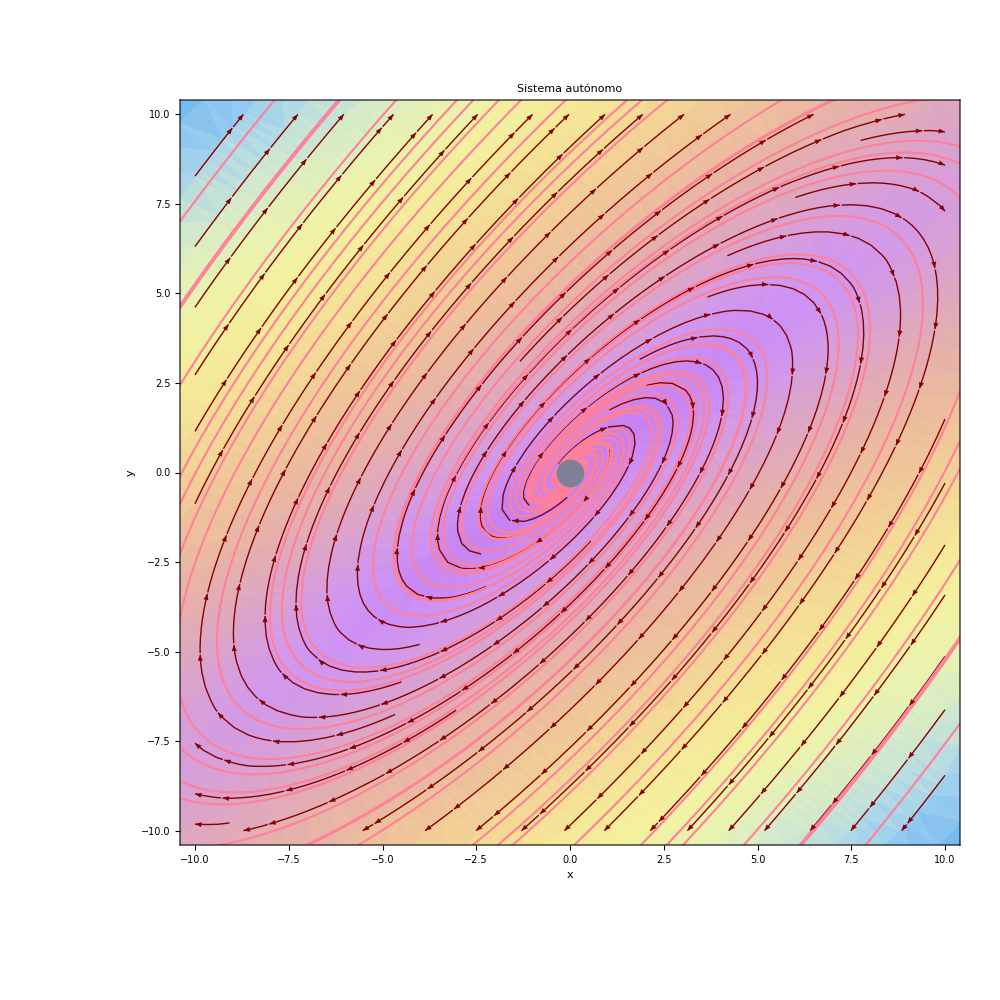

```mathematica
Showing[G12,G22](*Graficando el Retrato de fase y la singularidad*)
```

## Pregunta 3 : Dada la ecuación diferencial, escribela como un sistema autónomo plano, analizarlo en forma cualitativa y establecer el retrato de fase para el caso u≠0

La ecuación diferencial es :(ⅆ^2 x)/(ⅆ t^2)+μⅆx/ⅆt+25x=0
Derivando y reemplazando para transformar la ecuación diferencial en un sistema de ecuaciones con : x_1=x  y x_2=ẋ obtenemos:
Piecewise[{{OverDot[x_1], =x_2}, {OverDot[x_2], =-25 x_1-μ*x_2}}]

```mathematica
SetAttributes[u,Constant]
```

```mathematica
Clear[u]
```

Definiendo las funciones componentes del campo vectorial asociado al sistema:

```mathematica
f3[x1_,x2_]:=x2;
```

```mathematica
g3[x1_,x2_]:=-25x1-u*x2;
```

Ubicando las singularidades:

```mathematica
Solve[{f3[x1,x2]==0,g3[x1,x2]==0}]
```

{{x1→0,x2→0}}

En este caso solo hay una singularidad y esta en el origen.
		Analizando la estabilidad del origen, de acuerdo a la naturaleza de los vectores propios de la matriz A del sistema autónomo:

```mathematica
A3=({{0, 1}, {-25, -u}});
```

```mathematica
Eigenvalues[A3]
```

{1/2 (-u-√(-100+u^2)),1/2 (-u+√(-100+u^2))}

```mathematica
Eigenvectors[A3]
```

{{1/50 (-u+√(-100+u^2)),1},{1/50 (-u-√(-100+u^2)),1}}

Observamos que los autovalores y autovectores dependen de la naturaleza de u.
		Entonces, definiendo u=0 :

```mathematica
u=0;
Eigensystem[A3]
```

{{5 ⅈ,-5 ⅈ},{{-ⅈ,5},{ⅈ,5}}}

Observamos que los autovalores son complejos de valores conjugados y la parte real es cero, por lo cual deducimos que la singularidad del 			origen es de tipo centro.

```mathematica
G13=LinCam[f3,g3,10];(*Graficando lineas de corriente Streamlines*)
```

```mathematica
G23=RetFas[f3,g3];(*Graficando el ciertas soluciones - Retrato de fase*)
```

```mathematica
Showing[G13,G23](*Graficando el Retrato de fase y la singularidad*)
```

-Graphics-